```mathematica
Clear["Global`*"]
Needs["ErrorBarPlots`"]
fermi = 1;
If[fermi == 1,SetDirectory[StringJoin[NotebookDirectory[],"/Fermions"]],SetDirectory[StringJoin[NotebookDirectory[],"/Bosons"]]];
nbeads = 2;
nd = 3;
npart = 5;
firstbead = 64; 
duration = 18000;
halfspace = 1;
bisect = 0;
βmin=1;
nβ=10;
dβ=1;
beadexp = Log[2,firstbead];
```

```mathematica
For[j=0,j<nβ,j++,For[i=0,i<nbeads,i++,points[i][j]=Import[StringJoin["sgnTrace",ToString[npart],"-",ToString[nd],"-",ToString[2^(i+beadexp)],"-",ToString[βmin+j dβ],"-",ToString[duration],"-",ToString[fermi],"-",ToString[halfspace],"-",ToString[bisect],".txt"],"Table"]]]
```

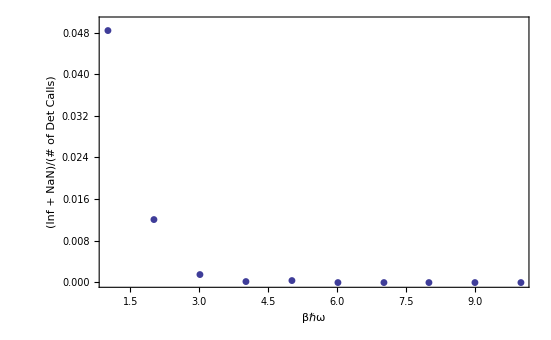

```mathematica
bead=1;
infnanPlot=ListPlot[Table[(points[bead][j][[2,1]]+points[bead][j][[2,2]])/(points[bead][j][[1,2]]+points[bead][j][[1,3]])*1.0,{j,0,nβ-1}],PlotStyle->Thick,PlotMarkers-> Automatic];
Show[infnanPlot,LabelStyle->Directive[FontFamily->"Helvetica"],RotateLabel-> False,Frame->True,FrameLabel-> {Style["βℏω",Bold],Style["(Inf  +  NaN)/(# of Det Calls)",Bold]},PlotRange-> {0,0.05}]
```